# Cálculo de Linhas de Campo Magnetostático

## Antonio Carlos Siqueira de Lima Outubro de 2008

```mathematica
(* length of a vector *)
norm[vector_] := Sqrt[vector.vector]
(* normalizing vectors *)
𝓃[vector_] := vector/Sqrt[vector.vector]
```

```mathematica
makeContours[ContourGraphics[data_, ___], n_] := 
With[{λ = Sort[Flatten[data]]}, 
     (* generate about n equal length sets *)
     #[[Floor[Length[λ]/n/2]]]& /@ 
              Partition[λ, Floor[Length[λ]/n]]]
```

```mathematica
makeFieldComponentDefinitions[
       fieldComponents_, field_, vars_, varType___] :=
((* remove existing definitions *)
 Clear /@ fieldComponents;
 (* create new definitions *)
 MapIndexed[(SetDelayed @@ 
             (Hold[#1[Pattern[#, Blank[varType]]& /@ vars], 
                   𝓃[field[vars]][[C]]] /. C -> #2[[1]]))&,
            fieldComponents])
```

```mathematica
orthogonalDirections[{p1_, p2_, p3_}] :=
Module[{𝒹}, 
       If[Abs[#1.#2] == 1, (* parallel case *)
          𝒹 = If[Abs[#1[[3]]] < 1, {-#1[[2]], #1[[1]], 0}, 
                 {0, #1[[3]], -#1[[2]]}], 
          𝒹 = (#1 + #2)/2];
          𝓃 /@ {𝒹, Cross[#1, 𝒹]}]&[𝓃[p3 - p2], 𝓃[p1 - p2]];
```

```mathematica
calculateFieldLine[fieldLineVector_, startPoint_, 
                   fields_, {t, t0_:0, t1_}, opts___] :=
With[{flvt = #[t]& /@ fieldLineVector},               
NDSolve[Join[(* differential equation *)
             Thread[D[flvt, t] == (#[flvt]& /@ fields)],
             (* initial conditions *)
             Thread[(flvt /. t -> t0) == startPoint]],
        fieldLineVector, {t, t0, t1}, opts]]
```

```mathematica
fieldLineGraphic[cxcy_] := 
ParametricPlot[Evaluate[{cx[t], cy[t]} /. cxcy], 
               Evaluate[Flatten[{t, cxcy[[1, 1, 2, 1, 1]]}]],
               PlotPoints -> 300, DisplayFunction -> Identity]
```

```mathematica
(* fl["+" -> "-"] = fieldLineGraphic /@ fieldLines["+" -> "-"]; *)
```

```mathematica
makeTube[Line[points_], startCrossSection_, rFunction_] := 
MapThread[Polygon[Join[#1, Reverse[#2]]]&, #1]& /@ 
(Map[Partition[#, 2, 1]&, Partition[
MapIndexed[(* change tube diameter *)
           rFunction[#1, #2, Length[points]]&, 
FoldList[Function[{p, t}, 
Module[{o = orthogonalDirections[t]},  
       (* move along the line *)
       prolongate[#, t[[2]], t[[2]] - t[[1]], o]& /@ p]],
       startCrossSection, 
       Rest[Partition[points, 3, 1]]]], 2, 1], {2}]);
```

```mathematica
prolongate[p_, q_, 𝒹_, {dirx_, diry_}] := 
Module[{s, u, v}, First[p + s 𝒹 /. 
       Solve[Thread[(* line intersects plane *)
                    p + s 𝒹 == q + u dirx + v diry], {s, u, v}]]];
```

We will change the diameter of the tubes in such a way that at the starting and ending points of the corresponding lines, they thin out. The function ρFunc determines the tube diameter along the line.

```mathematica
ρFunc[l_, {pos_}, n_] := 
Function[mp, mp + Sin[(pos - 1)/(n - 1) Pi]^2 *
            (# - mp)& /@ l][(* cross-section center *)
               (Plus @@ Rest[l])/(Length[l] - 1)]
```

The function tubeGraphics3D calculates the tubes.

```mathematica
tubeGraphics3D[line_Line, {r_:0.015, rFunction_:(#1&)},
               color_, startCrossSection_:Automatic] :=
Module[{dir, dir1, dir2, scs, ppSCS = 12},
If[startCrossSection === Automatic,
   (* make start cross section *)
   dir = 𝓃[line[[1, 2]] - line[[1, 1]]];
   dir1 = 𝓃[# - # dir]&[Table[Random[], {3}]];
   dir2 = 𝓃[Cross[dir, dir1]];
   scs = Table[N[line[[1, 1]] + r (Cos[φ] dir1 + Sin[φ] dir2)],
			   {φ, 0, 2π, 2π/ppSCS}],
   scs = startCrossSection[[1]]];
Graphics3D[{EdgeForm[], color, (* make tube *)
makeTube[Line[Join[{line[[1, -2]]}, line[[1]],
                   {line[[1, 2]]}]], scs, rFunction]}]]
```

Using this function, we implement a function fieldLine3D that will convert an InterpolatingFunction representing the field line in a thin tube.

```mathematica
fieldLine3D[fieldLineIF_, color_] :=
Module[{tMax, n = 60},
tMax = DeleteCases[fieldLineIF[[1, 1, 2, 1, 1]], 0.][[1]];
If[Abs[tMax] > 0, 
   tubeGraphics3D[Line[Table[Evaluate[{cx[t], cy[t], cz[t]} /. 
       fieldLineIF[[1]]], {t, 0, tMax, tMax/n}]], 
                  {0.016, ρFunc}, color], {}]]
```

```mathematica
infiniteWire[t_] = {0, 0, t};
```

Using the Biot–Savart law, we obtain the well-known magnetic field B⃗(x⃗)∼{-y,x,0}/(x^2+y^2).

```mathematica
Integrate[Cross[D[infiniteWire[t], t], {x, y, z} - infiniteWire[t]]/
                norm[{x, y, z} - infiniteWire[t]]^3, 
          {t, -Infinity, Infinity}, GenerateConditions -> False]
```

{-(2 y)/(x^2+y^2),(2 x)/(x^2+y^2),0}

```mathematica
BInfiniteWire[{x_, y_}] =  {-y, x}/(x^2 + y^2);
```

Using the last result, we define the components of the magnetic field.

```mathematica
makeFieldComponentDefinitions[{Bx, By}, BInfiniteWire, {x, y}];
```

In the following example, we will display all current carrying wires as thin tubes with a yellow–orange color.

```mathematica
currentColor = SurfaceColor[Hue[0.12], Hue[0.22], 2.12];
```

For 12 randomly selected initial points, we calculate the field lines.

```mathematica
tMax = 12;
fieldLines = 
calculateFieldLine[{cx, cy}, #, {Bx, By}, {t,-tMax, tMax},
           MaxSteps -> 10^4]& /@ Table[Random[], {12}, {2}];
```

As expected, the field lines are concentric circles around the infinite wire. (For particle trajectories in the magnetic field of a long straight current-carrying wire, see [1349✶].)

```mathematica
Show[{tubeGraphics3D[Line[{{0, 0, -1}, {0, 0, 0}, {0, 0, 1}}], 
                     {}, currentColor],
ParametricPlot3D[Evaluate[{cx[t], cy[t], 0, 
          {Thickness[0.002]}} /. #], {t, 0, tMax}, 
          PlotPoints -> 200, PlotRange -> All,
          DisplayFunction -> Identity]& /@ fieldLines},
          DisplayFunction -> $DisplayFunction]
```

-Graphics3D-

## Duas correntes de mesmo sentido

Instead of one infinite straight current, let us now deal with many of them. We choose 15 parallel currents at random positions and of random strengths. This system is translation-invariant along the wires. So, we restrict ourselves to the plane z=0.

```mathematica
xy2={{-1,0},{1,0}};
```

```mathematica
(* SeedRandom[83569034823]
BField[{x_, y_}] = Plus @@ 
((Random[Real, {-1, 1}] BInfiniteWire[{x, y} - #])& /@ 
  (mps = Table[{Random[Real], Random[Real]}, {15}])) *)
```

```mathematica
BField[{x_, y_}] = Plus @@ 
(( BInfiniteWire[{x, y} - #])& /@ 
  (xy2))
```

{-y/((-1+x)^2+y^2)-y/((1+x)^2+y^2),(-1+x)/((-1+x)^2+y^2)+(1+x)/((1+x)^2+y^2)}

```mathematica
BFieldC = Compile[{x, y}, Evaluate[BField[{x, y}]]];
```

```mathematica
BField[{x_, y_}] := BFieldC[x, y]
```

```mathematica
makeFieldComponentDefinitions[{Bx, By}, BField, {x, y}, Real];
```

```mathematica
tMax = 10;
(fieldLines = 
 Table[calculateFieldLine[{cx, cy},
           {Random[], Random[]}, {Bx, By}, {t, tMax},
            MaxSteps -> 10^4, Compiled -> False,
            AccuracyGoal -> 6, PrecisionGoal -> 6], {30}];) // Timing
```

{0.78,Null}

```mathematica
Dimensions[Evaluate[{cx[t],cy[t]}/.fieldLines]]
```

{30,1,2}

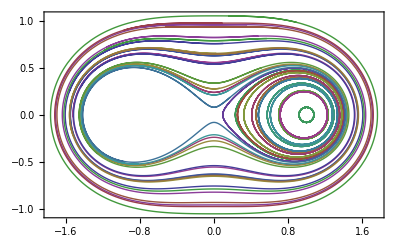

```mathematica
ParametricPlot[Evaluate[{cx[t],cy[t]}/.fieldLines],{t,0,tMax},PlotPoints->20,Axes->False,Frame->True]
```

```mathematica
Export["F:\\TE_I_2008-2\\h2condiguaisdetail.pdf", %]
```

F:\TE_I_2008-2\h2condiguaisdetail.pdf

## Duas correntes de sentidos contrários

Instead of one infinite straight current, let us now deal with many of them. We choose 15 parallel currents at random positions and of random strengths. This system is translation-invariant along the wires. So, we restrict ourselves to the plane z=0.

```mathematica
xy2={{-1,0},{1,0}};
```

```mathematica
(* SeedRandom[83569034823]
BField[{x_, y_}] = Plus @@ 
((Random[Real, {-1, 1}] BInfiniteWire[{x, y} - #])& /@ 
  (mps = Table[{Random[Real], Random[Real]}, {15}])) *)
```

```mathematica
BField2[{x_,y_}]={-y/((x-1)^2+(y)^2)+y/((x+1)^2+y^2),(x-1)/((x-1)^2+y^2)-(x+1)/((x+1)^2+y^2)}
```

{-y/((-1+x)^2+y^2)+y/((1+x)^2+y^2),(-1+x)/((-1+x)^2+y^2)-(1+x)/((1+x)^2+y^2)}

```mathematica
BFieldC2 = Compile[{x, y}, Evaluate[BField2[{x, y}]]];
```

```mathematica
BField2[{x_, y_}] := BFieldC2[x, y]
```

```mathematica
makeFieldComponentDefinitions[{Bx, By}, BField2, {x, y}, Real];
```

```mathematica
tMax = 50;
(fieldLines = 
 Table[calculateFieldLine[{cx, cy},
           {Random[], Random[]}, {Bx, By}, {t, -tMax,tMax},
            MaxSteps -> 10^4, Compiled -> False,
            AccuracyGoal -> 6, PrecisionGoal -> 6], {20}];) // Timing
```

{0.858,Null}

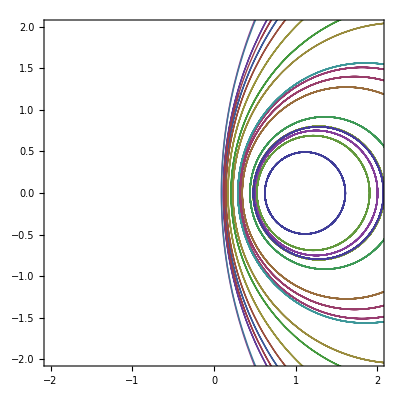

```mathematica
o1=ParametricPlot[Evaluate[{cx[t],cy[t]}/.fieldLines],{t,0,tMax},PlotPoints->20,Axes->False,Frame->True,PlotRange-> {{-2,2},{-2,2}}]
```

```mathematica
Export["F:\\te_i_2008-2/h2condcontdetail.pdf",o1]
```

F:\te_i_2008-2/h2condcontdetail.pdf

## Com diversas correntes de mesma intensidade

```mathematica
mps = Table[{Cos[60 Degree i],Sin[60 Degree i]}, {i,0,5}]
```

{{1,0},{1/2,(√3)/2},{-1/2,(√3)/2},{-1,0},{-1/2,-(√3)/2},{1/2,-(√3)/2}}

```mathematica
BField[{x_, y_}] = Plus @@ 
( BInfiniteWire[{x, y} - #]& /@ mps );
```

```mathematica
BFieldC = Compile[{x, y}, Evaluate[BField[{x, y}]]];
BField[{x_, y_}] := BFieldC[x, y]
makeFieldComponentDefinitions[{Bx, By}, BField, {x, y}, Real];
```

```mathematica
tMax = 50;
(fieldLines = 
 Table[calculateFieldLine[{cx, cy},
           {Random[], Random[]}, {Bx, By}, {t, tMax},
            MaxSteps -> 10^4, Compiled -> False,
            AccuracyGoal -> 6, PrecisionGoal -> 6], {20}];) // Timing
```

{5.32,Null}

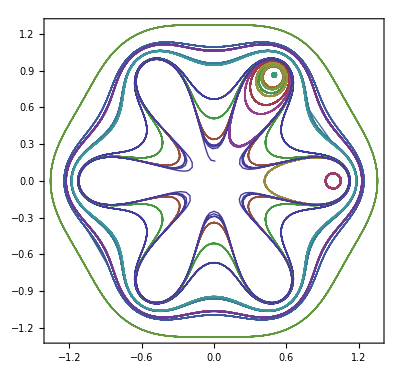

```mathematica
ParametricPlot[Evaluate[{cx[t],cy[t]}/.fieldLines],{t,0,tMax},PlotPoints->20,Axes->False,Frame->True]
```

```mathematica
Export["F:\\TE_I_2008-2\h6condiguaisdetail.pdf",%]
```

F:\TE_I_2008-2\h6condiguaisdetail.pdf

```mathematica
BField6[{x_, y_}] ={-y/((-1+x)^2+y^2)+y/((1+x)^2+y^2)-(-(√3)/2+y)/((-1/2+x)^2+(-(√3)/2+y)^2)+(-(√3)/2+y)/((1/2+x)^2+(-(√3)/2+y)^2)-((√3)/2+y)/((-1/2+x)^2+((√3)/2+y)^2)+((√3)/2+y)/((1/2+x)^2+((√3)/2+y)^2), (-1+x)/((-1+x)^2+y^2)-(1+x)/((1+x)^2+y^2)+(-1/2+x)/((-1/2+x)^2+(-(√3)/2+y)^2)-(1/2+x)/((1/2+x)^2+(-(√3)/2+y)^2)+(-1/2+x)/((-1/2+x)^2+((√3)/2+y)^2)-(1/2+x)/((1/2+x)^2+((√3)/2+y)^2)};
```

```mathematica
BFieldC = Compile[{x, y}, Evaluate[BField6[{x, y}]]];
BField6[{x_, y_}] := BFieldC[x, y]
makeFieldComponentDefinitions[{Bx, By}, BField6, {x, y}, Real];
```

```mathematica
tMax = 50;
(fieldLines = 
 Table[calculateFieldLine[{cx, cy},
           {Random[], Random[]}, {Bx, By}, {t, tMax},
            MaxSteps -> 10^4, Compiled -> False,
            AccuracyGoal -> 6, PrecisionGoal -> 6], {20}];) // Timing
```

{1.965,Null}

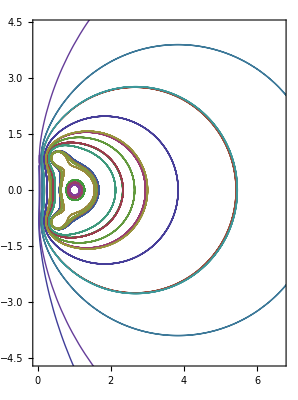

```mathematica
ParametricPlot[Evaluate[{cx[t],cy[t]}/.fieldLines],{t,0,tMax},PlotPoints->20,Axes->False,Frame->True]
```

```mathematica
Export["F:\\TE_I_2008-2\\h6ccont.pdf", %]
```

F:\TE_I_2008-2\h6ccont.pdf

## Apelando para as funções já definidas no Mma

```mathematica
Needs["VectorFieldPlots`"]
```

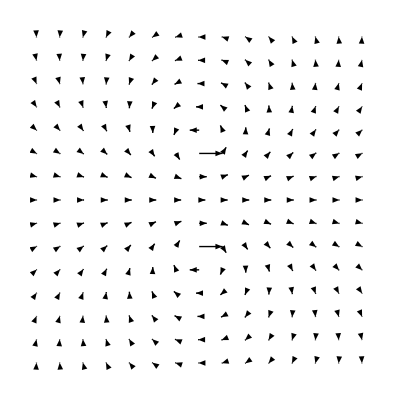

```mathematica
VectorFieldPlot[{-(-1+y)/(x^2+(-1+y)^2)+(1+y)/(x^2+(1+y)^2),x/(x^2+(-1+y)^2)-x/(x^2+(1+y)^2)},{x,-3,3},{y,-3,3}]
```

## Com diversas correntes aleatórias

```mathematica
SeedRandom[83569034823]
BField[{x_, y_}] = Plus @@ 
((Random[Real, {-1, 1}] BInfiniteWire[{x, y} - #])& /@ 
  (mps = Table[{Random[Real], Random[Real]}, {6}]))
```

{(0.746852 (-0.915544+y))/((-0.208538+x)^2+(-0.915544+y)^2)-(0.112032 (-0.840705+y))/((-0.773671+x)^2+(-0.840705+y)^2)+(0.433501 (-0.555042+y))/((-0.278772+x)^2+(-0.555042+y)^2)+(0.115256 (-0.246585+y))/((-0.000444648+x)^2+(-0.246585+y)^2)+(0.486329 (-0.225313+y))/((-0.313551+x)^2+(-0.225313+y)^2)+(0.785583 (-0.213914+y))/((-0.587299+x)^2+(-0.213914+y)^2),-(0.746852 (-0.208538+x))/((-0.208538+x)^2+(-0.915544+y)^2)+(0.112032 (-0.773671+x))/((-0.773671+x)^2+(-0.840705+y)^2)-(0.433501 (-0.278772+x))/((-0.278772+x)^2+(-0.555042+y)^2)-(0.115256 (-0.000444648+x))/((-0.000444648+x)^2+(-0.246585+y)^2)-(0.486329 (-0.313551+x))/((-0.313551+x)^2+(-0.225313+y)^2)-(0.785583 (-0.587299+x))/((-0.587299+x)^2+(-0.213914+y)^2)}

```mathematica
BFieldC = Compile[{x, y}, Evaluate[BField[{x, y}]]];
```

```mathematica
BField[{x_, y_}] := BFieldC[x, y]
```

```mathematica
makeFieldComponentDefinitions[{Bx, By}, BField, {x, y}, Real];
```

```mathematica
tMax = 20;
(fieldLines = 
 Table[calculateFieldLine[{cx, cy},
           {Random[], Random[]}, {Bx, By}, {t, tMax},
            MaxSteps -> 10^4, Compiled -> False,
            AccuracyGoal -> 6, PrecisionGoal -> 6], {100}];) // Timing
```

```mathematica
ParametricPlot[Evaluate[{cx[t],cy[t]}/.fieldLines],{t,0,tMax},PlotPoints->150,Axes->False,Frame->True]
```

{37.889,-Graphics-}